```mathematica
Lm =3; Ln = 3;
a=1.0;
```

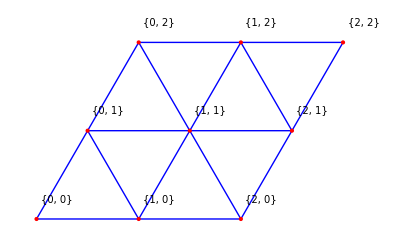

```mathematica
Graphics[Module[{points,bonds,labels,basis1,basis2,coord,indexMap,neighbors,validQ},basis1={a,0};
basis2=a*{1/2,Sqrt[3]/2};
coord[m_,n_]:=m*basis1+n*basis2;
points=Flatten[Table[{m,n},{m,0,Lm-1},{n,0,Ln-1}],1];
indexMap=AssociationThread[points->(coord@@@points)];
neighbors={{1,0},{0,1},{-1,1},{-1,0},{0,-1},{1,-1}};
validQ[{m_,n_}]:=0<=m<Lm&&0<=n<Ln;
bonds=DeleteDuplicates[Sort/@Reap[Do[Do[With[{dx=neighbor[[1]],dy=neighbor[[2]]},Module[{p1={m,n},p2={m+dx,n+dy}},If[validQ[p2],Sow[{indexMap[p1],indexMap[p2]}]]]],{neighbor,neighbors}],{m,0,Lm-1},{n,0,Ln-1}]][[2,1]]];
labels=Table[Text[Style[ToString[{m,n}],10],coord[m,n]+{0.2,0.2}],{m,0,Lm-1},{n,0,Ln-1}];
{Blue,Line/@bonds,Red,PointSize[Large],Point/@Values[indexMap],Black,labels}],Axes->False,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
bonds
```

{{{0,0},{1,0}},{{0,1},{1,1}},{{0,2},{1,2}},{{1,0},{2,0}},{{1,1},{2,1}},{{1,2},{2,2}},{{0,0},{0,1}},{{0,1},{0,2}},{{1,0},{1,1}},{{1,1},{1,2}},{{2,0},{2,1}},{{2,1},{2,2}}}

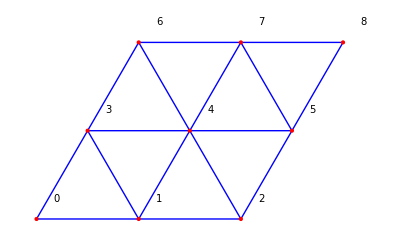

```mathematica
Graphics[Module[{points,bonds,labels,basis1,basis2,coord,indexMap,neighbors,validQ,indexedPoints},basis1={a,0};
basis2=a*{1/2,Sqrt[3]/2};
coord[m_,n_]:=m*basis1+n*basis2;
(*All lattice sites*)points=Flatten[Table[{m,n},{n,0,Ln-1},{m,0,Lm-1}],1];
(*Assign integer index to each point (row-major order)*)indexedPoints=AssociationThread[points->Range[0,Length[points]-1]];
(*Map (m,n) to real-space coordinates*)indexMap=AssociationThread[points->(coord@@@points)];
(*Triangular lattice neighbors*)neighbors={{1,0},{0,1},{-1,1},{-1,0},{0,-1},{1,-1}};
validQ[{m_,n_}]:=0<=m<Lm&&0<=n<Ln;
(*Generate bonds using real-space positions*)bonds=DeleteDuplicates[Sort/@Reap[Do[Do[With[{dx=neighbor[[1]],dy=neighbor[[2]]},Module[{p1={m,n},p2={m+dx,n+dy}},If[validQ[p2],Sow[{indexMap[p1],indexMap[p2]}]]]],{neighbor,neighbors}],{m,0,Lm-1},{n,0,Ln-1}]][[2,1]]];
(*Labels using integer site index*)labels=Table[Text[Style[ToString[indexedPoints[{m,n}]],10],indexMap[{m,n}]+{0.2,0.2}],{n,0,Ln-1},{m,0,Lm-1}];
{Blue,Line/@bonds,Red,PointSize[Large],Point/@Values[indexMap],Black,Flatten[labels]}],Axes->False,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
(*Convert bonds to integer-labeled format*)
integerBonds=Sort/@(indexMap/@#&/@bonds);
integerBonds
Length[integerBonds]
```

{{0,1},{3,4},{6,7},{1,2},{4,5},{7,8},{0,3},{3,6},{1,4},{4,7},{2,5},{5,8}}

12

```mathematica
(*periodicity*)

(*Define site index:row-major ordering*)

(*Integer site index in row-major order*)
siteIndex[m_,n_]:=Mod[m,Lm]+Lm*Mod[n,Ln];

(*6 nearest-neighbor triangular directions*)
neighbors={{1,0},(*right*){0,1},(*up-right*){-1,1},(*up-left*){-1,0},(*left*){0,-1},(*down-left*){1,-1}    (*down-right*)}; 

(*Generate triangular-lattice bonds with optional periodicity*)
generateTriangularBonds[periodicM_,periodicN_]:=Module[{wrapM,wrapN,bonds={},m2,n2},wrapM[m_]:=If[periodicM,Mod[m,Lm],If[0<=m<Lm,m,Nothing]];
wrapN[n_]:=If[periodicN,Mod[n,Ln],If[0<=n<Ln,n,Nothing]];
Do[Do[{dx,dy}=offset;
m2=wrapM[m+dx];
n2=wrapN[n+dy];
If[m2=!=Nothing&&n2=!=Nothing,AppendTo[bonds,Sort[{siteIndex[m,n],siteIndex[m2,n2]}]]],{offset,neighbors[[1;;3]]} (*3 directions to avoid double counting*)],{n,0,Ln-1},{m,0,Lm-1}];
DeleteDuplicates[bonds]];

(*Generate bond lists*)
bondsPBCm=generateTriangularBonds[True,False];
bondsPBCn=generateTriangularBonds[False,True];
bondsPBCboth=generateTriangularBonds[True,True];

(*Print outputs*)
Print["Triangular lattice: PBC in m only"];
bondsPBCm//Print;
Length[bondsPBCm]//Print;

Print["Triangular lattice: PBC in n only"];
bondsPBCn//Print;
Length[bondsPBCn]//Print;

Print["Triangular lattice: PBC in both m and n"];
bondsPBCboth//Print;
Length[bondsPBCboth]//Print;
```

Triangular lattice: PBC in m only

{{0,1},{0,3},{0,5},{1,2},{1,4},{1,3},{0,2},{2,5},{2,4},{3,4},{3,6},{3,8},{4,5},{4,7},{4,6},{3,5},{5,8},{5,7},{6,7},{7,8},{6,8}}

21

Triangular lattice: PBC in n only

{{0,1},{0,3},{1,2},{1,4},{1,3},{2,5},{2,4},{3,4},{3,6},{4,5},{4,7},{4,6},{5,8},{5,7},{6,7},{0,6},{7,8},{1,7},{0,7},{2,8},{1,8}}

21

Triangular lattice: PBC in both m and n

{{0,1},{0,3},{0,5},{1,2},{1,4},{1,3},{0,2},{2,5},{2,4},{3,4},{3,6},{3,8},{4,5},{4,7},{4,6},{3,5},{5,8},{5,7},{6,7},{0,6},{2,6},{7,8},{1,7},{0,7},{6,8},{2,8},{1,8}}

27